```mathematica
a [p0_, W_, w_] := -(W^2+w^2)/W*p0
```

{{p→Function[{t},Cos[t]],r→Function[{t},w Sin[t]]}}

{{True,True,True,True}}

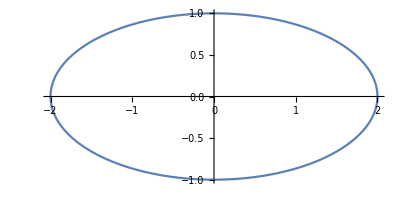

```mathematica
eqns = {r'[t] == w*p[t], p'[t] == w*r[t] +a[1, 1, w]*Sin[t], p[0] == 1, r[0] == 0};
sol = DSolve[eqns, {r, p}, t]
Simplify[eqns/. sol]
ParametricPlot[{r[t]/. sol[[1]] /. w->2, p[t] /. sol[[1]] /. w->2} , {t, -3.14, 3.14}]
```

Nota che questa cosa funziona solo con r0 = 0. Anche per valori leggermente diversi, le soluzioni divergono molto rapidamente. Questo spiega come mai non funziona il mio integratore numerico.

Solo per controllare che le soluzioni ottenute da noi siano corrette....

```mathematica
eqns1 = {r -> Function[{t},  Sinh[t] + a[1, 1, w]/(w^2+1)*(-w*Sin[t] + Sinh[w*t])], p ->Function[{t}, Cosh[t] + a[1, 1, w]/(w^2+1)*(-W*Cos[t] + Cosh[w*t])]}
Simplify[eqns/. (eqns1/.W->1)]
```

{r→Function[{t},Sinh[t]+(a[1,1,w] (-w Sin[t]+Sinh[w t]))/(w^2+1)],p→Function[{t},Cosh[t]+(a[1,1,w] (-W Cos[t]+Cosh[w t]))/(w^2+1)]}

{w Cosh[t]==Cosh[t],w Sinh[t]==Sinh[t],True,True}

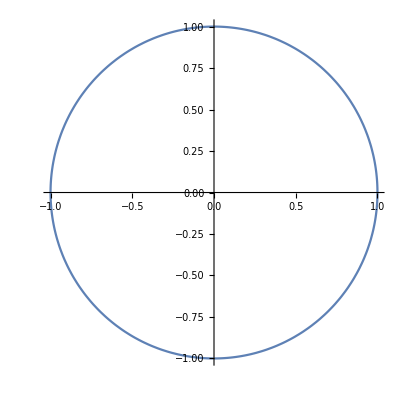

```mathematica
ParametricPlot[{r[t]/. eqns1 /. w->1 /. W->1, p[t] /. eqns1 /. w->1 /. W->1} , {t, -3.14, 3.14}]
```

Ok, probabilmente mancano qualche W e w che non ho inserito nelle formule. Il concetto però c’è.